```mathematica
1.0-2^-6
```

0.984375

```mathematica
(1-2.0^-5)*(1-2.0^-4)
```

0.908203

## Algorithm 4.1

### Code

#### Random Augmentation

Implementation of RandomOrthogonallyAugment.  Careful, it returns the augmented matrix: it returns the columns the old columns first followed by the new columns.  Used in 4 and 5.

```mathematica
RandOrth[{m_,s_}]:=Module[{V},
(* Using Simplest PRG and orthogonalizing *)
V=Orthogonalize[RandomReal[{-1,1},{s,m}]]ᵀ
]

RandOrthAug[U_,s_]:=Module[{m,n,V},
{m,n}=Dimensions[U];
(* Using Simplest PRG *)
(* No dimensioality testing for "space"  *)
(* for new orthogonal directions *)
V=RandomReal[{-1,1},{m,s}];
(* Orthogonalizing *)
V=Orthogonalize[(V-U.Uᵀ.V)ᵀ]ᵀ;
(* Augmenting the basis *)
ArrayFlatten[{{U,V}}]
]
```

Testing.

```mathematica
{m,s0,s1}={123,12,4};
U=RandOrth[{m,s0}];
V=RandOrthAug[U,s1];
Norm[Vᵀ.V-IdentityMatrix[s0+s1]]
```

8.6247×10^-16

Notes: It should not make any difference if I switch out the sample to a N[0,1] variant.

#### Sample

Assembles the block matrix in 6. Lower case phi and pi are Tall Skinny (TS) orthogonal matrices:  lower case to avoid Mathematica namespace collisions.

```mathematica
Sample[A_,{U_,S_,V_},{phi_,pi_}]:= {Uᵀ.A.pi,phiᵀ.A.V,phiᵀ.A.pi}
```

#### Algorithm 4.1

```mathematica
Algorithm4Point1Initialization[A_,{sl_,sr_}]:=Module[
{m,n,U0,V0,TwoSidedSample,U,S,V},
{m,n}=Dimensions[A];
(* Generates orthogonal sampler matrices *)
U0=RandOrth[{m,sl}];V0=RandOrth[{n,sr}];
(* Computes initial sample *)
TwoSidedSample=U0ᵀ.A.V0;
(* compute the SVD *)
{U,S,V}=SingularValueDecomposition[TwoSidedSample,Min[sl,sr]];
(* return the embedded SVD *)
{U0.U,S,V0.V}
]
```

```mathematica
Algorithm4Point1Step[A_,{U_,S_,V_},{sl_,sr_}]:=Module[
{phi,pi,UTApi, phiTAV, phiTApi,lambda, UNew, SNew,VNew},
(* Generates supplementary sample matrices *)
phi=RandOrthAug[U,sl];
pi=RandOrthAug[V,sr];
(* Generates supplementary samples *)
{UTApi, phiTAV, phiTApi}=Sample[A,{U,S,V},{phi,pi}];
Print["YY",Map[Dimensions,{UTApi, phiTAV, phiTApi}]];
(* Assembles update matrix *)
XX=({{S, UTApi}, {phiTApi, phiTApi}});
lambda=ArrayFlatten[({{S, UTApi}, {phiTApi, phiTApi}})];
{UNew,SNew,VNew}=SingularValueDecomposition[lambda];
{U.UNew}
]
```

Test the initializer.

```mathematica
{m,n}={123,72};
A=RandomReal[{-1,1},{m,n}];
{sl0,sr0}={3,4};
{U0,S0,V0}=Algorithm4Point1Initialization[A,{sl0,sr0}];
rank=Min[sl0,sr0]
Map[Norm, {U0ᵀ.A.V0-S0,U0ᵀ.U0-IdentityMatrix[rank],V0ᵀ.V0-IdentityMatrix[rank]}];
```

3

Test the stepper.

```mathematica
{m,n}={123,72};
A=RandomReal[{-1,1},{m,n}];
{sl0,sr0}={3,4};
{U0,S0,V0}=Algorithm4Point1Initialization[A,{sl0,sr0}];
Map[Dimensions,{U0,S0,V0}];
{sl,sr}={6,4};
Algorithm4Point1Step[A,{U0,S0,V0}, {sl,sr}];
Map[Dimensions,XX[[1]]]
Map[Dimensions,XX[[2]]]
```

YY{{3,4},{6,3},{6,4}}

ArrayFlatten::match: ArrayFlatten[{{{{1.59247,0.,0.},{0.,1.36086,0.},{0.,0.,0.378554}},{{1.32264,-0.290908,-0.362789,0.402332},{0.426781,-0.44428,-0.361508,-0.238775},{-0.881562,-0.174926,-0.464598,0.277883}}},{{«1»},{«1»}}}] fails the matching condition for ArrayFlatten[a,n]: if b = a[[i_1,i_2,...,i_n]], c = a[[j_1,j_2,...,j_n]], Head[a] == Head[b] == Head[c], Length[Dimensions[b]] >= n, Length[Dimensions[c]] >= n, and i_k = j_k, then Dimensions[b][[k]] must equal Dimensions[c][[k]]. Here the condition fails for k = 2 and i_k = j_k = 1.

Set::shape: Lists {UNew$27128,SNew$27128,VNew$27128} and SingularValueDecomposition[ArrayFlatten[{{{{1.59247,0.,0.},{0.,1.36086,0.},{0.,0.,0.378554}},{{1.32264,-0.290908,-0.362789,0.402332},{0.426781,«2»,-0.238775},{-0.881562,-0.174926,-0.464598,0.277883}}},{{{«1»},«4»,{«1»}},«1»}}]] are not the same shape.

{{3,3},{3,4}}

{{6,4},{6,4}}

```mathematica
?SingularValueDecomposition
```

```mathematica
MatrixForm[Map[Dimensions,XX,{2}]]
```

((3
4) | (3
2)
(3
2) | (3
2))

```mathematica
Map[Dimensions,YY]
Dimensions[S0]
```

{{3,2},{3,4},{3,2}}

{3,4}

```mathematica
Dundreggan
```

```mathematica
¶
```

```mathematica
¶Test
```

Thread::tdlen: Objects of unequal length in {-0.139634,-0.0461796}+{0.139634,0.0461796,-0.0457287,0.0671304,-0.0592943} cannot be combined.

Thread::tdlen: Objects of unequal length in {-0.0791894,-0.000838763}+{0.0791894,0.000838763,-0.0986311,-0.0671399,-0.0176403} cannot be combined.

Thread::tdlen: Objects of unequal length in {0.127759,-0.115301}+{-0.127759,0.115301,0.0411603,-0.12945,0.137288} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

{{-0.139634,-0.0461796}+{0.139634,0.0461796,-0.0457287,0.0671304,-0.0592943},{-0.0791894,-0.000838763}+{0.0791894,0.000838763,-0.0986311,-0.0671399,-0.0176403},{0.127759,-0.115301}+{-0.127759,0.115301,0.0411603,-0.12945,0.137288},{-0.135154,-0.0236071}+{0.135154,0.0236071,-0.0416064,-0.0929551,0.0599898},{-0.0689152,0.104977}+{0.0689152,-0.104977,-0.0603654,0.0500518,-0.129054},{-0.0121552,0.148593}+{0.0121552,-0.148593,0.127883,0.111283,-0.0929392},{0.0330249,-0.0682086}+{-0.0330249,0.0682086,-0.133994,0.080833,0.117161},{0.0766711,-0.0401035}+{-0.0766711,0.0401035,-0.0411346,0.113684,0.00161685},{0.120214,0.0990306}+{-0.120214,-0.0990306,0.121843,0.0506299,-0.0827954},{0.0253166,0.043853}+{-0.0253166,-0.043853,-0.0696821,0.0894272,0.0979926},{-0.136822,-0.0867404}+{0.136822,0.0867404,0.0570013,-0.164021,-0.143693},{0.0804353,-0.121403}+{-0.0804353,0.121403,-0.120084,0.163395,0.0373582},{-0.0539228,0.158834}+{0.0539228,-0.158834,-0.0615563,-0.12145,0.0510984},{0.0737831,-0.0868175}+{-0.0737831,0.0868175,0.0427859,0.131128,-0.0397028},{-0.0115716,0.107343}+{0.0115716,-0.107343,-0.117021,-0.0553072,0.177005},{-0.108384,0.162804}+{0.108384,-0.162804,-0.12069,0.129303,-0.0670517},{0.0778667,-0.0363679}+{-0.0778667,0.0363679,-0.0889343,-0.0794476,-0.0692888},{-0.143298,-0.0521822}+{0.143298,0.0521822,-0.101981,0.107003,0.151439},{0.0588683,-0.00775121}+{-0.0588683,0.00775121,-0.0630431,-0.000363414,0.0709092},{0.0462608,0.141089}+{-0.0462608,-0.141089,-0.127273,-0.0314825,0.0146232},{0.0737239,0.147141}+{-0.0737239,-0.147141,-0.00340807,0.0800561,0.0856469},{-0.0175751,0.09691}+{0.0175751,-0.09691,-0.00957942,-0.00796474,0.134296},{0.124555,-0.000679276}+{-0.124555,0.000679276,-0.0661464,0.0603941,0.0253925},{-0.114706,0.0857672}+{0.114706,-0.0857672,-0.10103,0.129177,-0.0973069},{0.0264133,0.0118308}+{-0.0264133,-0.0118308,0.123248,0.144231,0.0452604},{0.0349773,0.146988}+{-0.0349773,-0.146988,0.129693,0.0544731,-0.0310432},{-0.110183,-0.0515218}+{0.110183,0.0515218,-0.145718,0.055393,0.0176234},{0.0667921,0.0679136}+{-0.0667921,-0.0679136,0.136611,-0.0883037,-0.0865409},{0.01283,-0.10099}+{-0.01283,0.10099,-0.0972891,-0.0963329,-0.105881},{0.0630539,-0.0618479}+{-0.0630539,0.0618479,0.0887739,-0.0536816,0.0871344},{-0.0725024,0.0426931}+{0.0725024,-0.0426931,-0.0266523,0.00693736,0.129748},{-0.117651,0.154948}+{0.117651,-0.154948,0.08498,-0.0539142,-0.147372},{0.0979282,-0.0675426}+{-0.0979282,0.0675426,-0.0604707,-0.0660186,-0.135698},{-0.0601902,-0.0688546}+{0.0601902,0.0688546,-0.125463,-0.0262683,-0.129283},{0.028005,-0.0204661}+{-0.028005,0.0204661,-0.0689552,0.157211,-0.143321},{-0.118084,0.0794006}+{0.118084,-0.0794006,-0.12807,-0.0244665,0.0635523},{-0.146767,-0.103061}+{0.146767,0.103061,0.0987049,-0.0573228,-0.114168},{-0.0325,0.0195014}+{0.0325,-0.0195014,-0.116107,-0.000123742,0.027267},{-0.0485018,-0.0991442}+{0.0485018,0.0991442,0.0285406,0.10934,0.0850646},{-0.0423118,0.0435613}+{0.0423118,-0.0435613,0.118645,-0.073515,0.115798},{-0.0405057,0.162028}+{0.0405057,-0.162028,0.0718845,0.0536518,0.0144185},{-0.100407,-0.0629936}+{0.100407,0.0629936,-0.135921,0.0221716,0.0959726},{0.13947,-0.0874503}+{-0.13947,0.0874503,-0.131144,-0.121327,-0.0955545},{0.0537227,-0.141429}+{-0.0537227,0.141429,-0.0906308,-0.113552,-0.104144},{0.00555043,0.127427}+{-0.00555043,-0.127427,-0.105692,-0.0670129,0.00515161},{0.0547905,0.133958}+{-0.0547905,-0.133958,-0.125411,-0.146654,-0.0730625},{0.150849,0.108285}+{-0.150849,-0.108285,0.0860469,0.162655,0.119795},{0.101272,0.0429506}+{-0.101272,-0.0429506,-0.118332,0.0192324,-0.0398067},{0.14432,-0.0344076}+{-0.14432,0.0344076,-0.0552118,-0.142767,0.1579},{0.136365,-0.154245}+{-0.136365,0.154245,-0.0739431,-0.0213101,0.0917001},{0.074466,-0.0859848}+{-0.074466,0.0859848,0.0241618,0.0694923,-0.00189323},{-0.109248,0.0433106}+{0.109248,-0.0433106,-0.0310311,0.136877,0.0650528},{0.103451,0.103584}+{-0.103451,-0.103584,-0.112146,-0.121306,0.0156837},{0.0481033,-0.031245}+{-0.0481033,0.031245,0.0243083,0.148321,0.127967},{-0.00223793,-0.0747108}+{0.00223793,0.0747108,-0.0988362,0.146001,-0.0341832},{-0.0743492,-0.143877}+{0.0743492,0.143877,0.00323756,-0.0100293,0.0330288},{0.0230978,0.0431786}+{-0.0230978,-0.0431786,0.0899427,0.124477,0.0908369},{0.126663,-0.0643254}+{-0.126663,0.0643254,0.102031,-0.0248572,-0.149892},{0.0846363,0.0443562}+{-0.0846363,-0.0443562,0.136466,0.00352837,-0.16097},{0.0299827,0.0800198}+{-0.0299827,-0.0800198,-0.0497784,0.0631733,-0.111582},{0.0526018,0.116957}+{-0.0526018,-0.116957,-0.0990419,0.114363,0.0292574},{0.129949,0.134843}+{-0.129949,-0.134843,0.00296477,-0.00611464,-0.00467761},{-0.113933,-0.0883388}+{0.113933,0.0883388,-0.00804004,0.0360802,-0.0300928},{0.142317,0.117892}+{-0.142317,-0.117892,-0.0846135,-0.0203036,-0.111744},{0.0746924,0.130275}+{-0.0746924,-0.130275,0.106613,0.0184437,0.134914},{0.122791,0.0161708}+{-0.122791,-0.0161708,-0.0913251,0.158065,-0.0522976},{-0.0842243,0.0249915}+{0.0842243,-0.0249915,-0.117096,-0.0479066,0.120251},{-0.0832848,-0.121099}+{0.0832848,0.121099,0.0873919,0.0516624,-0.147567},{0.0959598,0.0761982}+{-0.0959598,-0.0761982,0.0609084,-0.0444523,0.0153199},{-0.0944906,0.0201822}+{0.0944906,-0.0201822,0.00270837,-0.127914,0.0466569},{-0.094099,-0.110941}+{0.094099,0.110941,-0.137363,0.0597026,-0.135719},{0.0728666,0.0395472}+{-0.0728666,-0.0395472,0.139597,0.0949574,0.027752},{0.0415535,0.124973}+{-0.0415535,-0.124973,0.0187752,-0.0307002,-0.136868},{-0.137493,-0.0478493}+{0.137493,0.0478493,0.0978074,0.0868587,-0.00769212},{0.146591,0.104973}+{-0.146591,-0.104973,-0.0959147,-0.0309326,-0.0597354},{0.139889,0.12164}+{-0.139889,-0.12164,-0.128301,0.00805956,0.0120934},{0.0586318,-0.0352311}+{-0.0586318,0.0352311,0.0784664,0.0488884,-0.0486436},{0.0922583,-0.118292}+{-0.0922583,0.118292,0.120524,0.158309,0.0572868},{-0.0707612,0.077905}+{0.0707612,-0.077905,0.096542,-0.146303,-0.103476},{0.124072,0.0243973}+{-0.124072,-0.0243973,0.0281263,-0.102013,-0.038787},{0.06216,0.0355906}+{-0.06216,-0.0355906,0.00883027,0.119643,-0.085608},{-0.0155127,0.0208479}+{0.0155127,-0.0208479,-0.0320592,-0.160226,0.149497},{0.129816,0.0977635}+{-0.129816,-0.0977635,-0.0837255,0.0520235,-0.0798426},{0.0695642,0.113516}+{-0.0695642,-0.113516,0.0720469,-0.0514208,0.128272},{0.0649339,0.123145}+{-0.0649339,-0.123145,-0.0160609,0.100981,0.139262},{0.0360209,-0.0256414}+{-0.0360209,0.0256414,-0.12309,0.0270918,0.0237762},{0.109837,0.0573551}+{-0.109837,-0.0573551,-0.0248229,-0.0847809,-0.0494683},{0.0354902,0.0270878}+{-0.0354902,-0.0270878,-0.120316,-0.075412,0.037904},{-0.103655,0.110096}+{0.103655,-0.110096,0.10549,-0.0794575,0.0123656},{-0.0233878,0.0567663}+{0.0233878,-0.0567663,-0.118518,0.12127,-0.0284101},{0.0117202,-0.14099}+{-0.0117202,0.14099,-0.0792733,-0.0417375,0.0878236},{-0.0582637,0.0555627}+{0.0582637,-0.0555627,0.0746817,-0.0746958,0.0950338},{-0.116323,0.120708}+{0.116323,-0.120708,0.0352052,0.0890213,0.0635573},{-0.125228,-0.0317782}+{0.125228,0.0317782,-0.0555159,0.136867,-0.0660621},{-0.107711,0.0435409}+{0.107711,-0.0435409,-0.0945974,-0.0197497,0.0984035},{0.0431877,-0.128684}+{-0.0431877,0.128684,-0.112218,-0.0025807,-0.0538937},{0.127434,-0.0117555}+{-0.127434,0.0117555,0.0189929,-0.0667171,-0.0260294},{-0.0944346,0.0594714}+{0.0944346,-0.0594714,0.0631537,-0.119012,0.0577321},{0.092469,-0.0507052}+{-0.092469,0.0507052,-0.0779377,0.12607,-0.00366805},{0.0846578,0.0498019}+{-0.0846578,-0.0498019,0.0678099,-0.0577675,0.0146319},{-0.0187763,-0.0128268}+{0.0187763,0.0128268,0.123169,0.0865067,0.096835},{-0.129006,-0.0314176}+{0.129006,0.0314176,-0.144179,0.040743,0.123794},{-0.136433,0.0927434}+{0.136433,-0.0927434,0.0319536,0.100415,0.120262},{-0.10357,0.151235}+{0.10357,-0.151235,-0.0463484,-0.00525467,-0.0878734},{0.133706,-0.120691}+{-0.133706,0.120691,0.110118,-0.0308726,0.0416557},{-0.0200446,0.141335}+{0.0200446,-0.141335,-0.0123332,-0.0959461,-0.0122478},{-0.0779358,0.00172683}+{0.0779358,-0.00172683,-0.0066155,0.116298,-0.11575},{0.0522132,0.0502972}+{-0.0522132,-0.0502972,-0.105105,-0.151771,-0.0863416},{-0.0179022,0.0863372}+{0.0179022,-0.0863372,-0.0912286,-0.00360247,-0.0636229},{0.0246831,0.0307523}+{-0.0246831,-0.0307523,-0.0254214,-0.117687,0.16256},{0.0929173,-0.0634657}+{-0.0929173,0.0634657,0.0847927,0.011866,0.0548546},{0.0420594,-0.13459}+{-0.0420594,0.13459,-0.0347345,-0.0738746,0.11261},{0.0845296,-0.0191836}+{-0.0845296,0.0191836,0.14337,0.0680216,0.0717738},{-0.112475,-0.0922044}+{0.112475,0.0922044,0.116146,-0.0705147,-0.0377511},{-0.0482949,0.0910062}+{0.0482949,-0.0910062,-0.118401,0.0316991,-0.111448},{0.0625008,0.0506106}+{-0.0625008,-0.0506106,-0.0702012,0.0695333,-0.00749117},{0.0490355,-0.145704}+{-0.0490355,0.145704,0.0617259,0.0369065,-0.0349728},{-0.114561,-0.0449807}+{0.114561,0.0449807,-0.0407981,-0.135921,0.115077},{0.116117,0.0221507}+{-0.116117,-0.0221507,-0.124365,0.106695,0.117856},{0.136674,-0.118232}+{-0.136674,0.118232,-0.0820974,-0.0972601,0.112973},{-0.0671637,-0.0373606}+{0.0671637,0.0373606,-0.0210543,0.0823514,0.0640092},{-0.113269,0.0978532}+{0.113269,-0.0978532,0.126894,-0.0838671,0.126156},{0.035537,0.110012}+{-0.035537,-0.110012,-0.0975496,-0.00406635,-0.022983}}

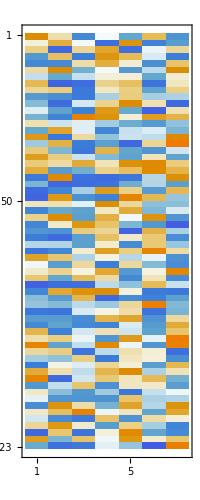

(1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.)

```mathematica
MatrixPlot[V]
MatrixForm[Chop[Vᵀ.V]]
```

## Half Normal Distribution.

I think this explains the spacing on some of the graphs from experiment one.

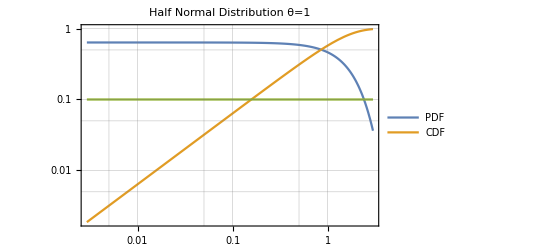

```mathematica
θ=1;
LogLogPlot[{(2 ⅇ^(-(x^2 θ^2)/π)θ)/π,Erf[(x θ)/(√π)],0.1},{x,0, 3},
PlotLegends->{"PDF","CDF"},
PlotLabel->StringForm["Half Normal Distribution θ=``",θ],
GridLines->Automatic,Frame->True]
```

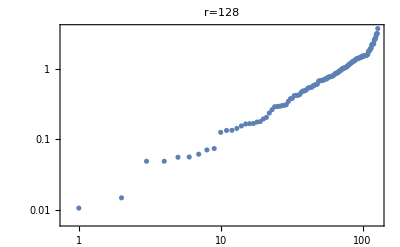

```mathematica
r=2^7;
ListLogLogPlot[
Sort[RandomVariate[HalfNormalDistribution[1],r]],
PlotRange->All,GridLines->Automatic,
PlotLabel->StringForm["r=``",r],
Frame->True]
```